Ananye Patel
UID: 404808384
ananye.97@gmail.com
PHYSICS 105A Mathematica HW 4

l m (g (-1.+Cos[th[t]])+0.5 l th'[t]^2)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{th→Function[{t},-2. JacobiAmplitude[(√(l C[1] (0.25 t^2+0.5 t C[2]+0.25 C[2]^2)+g (0.5 t^2+1. t C[2]+0.5 C[2]^2)))/(√l),(4. g)/(2. g+l C[1])]]},{th→Function[{t},2. JacobiAmplitude[(√(l C[1] (0.25 t^2+0.5 t C[2]+0.25 C[2]^2)+g (0.5 t^2+1. t C[2]+0.5 C[2]^2)))/(√l),(4. g)/(2. g+l C[1])]]}}

{th→InterpolatingFunction[…]}

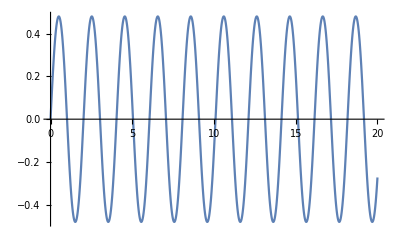

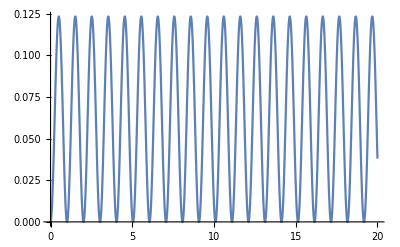

```mathematica
(* Question 1 *)
Remove["Global`*"]
	(*i*)
SetAttributes[{m,l,g},Constant]
T=0.5*m*((Dt[x[t],t])^2+(Dt[y[t],t])^2);U=m*g*y[t];
	(*ii*)
LG=T-U//FullSimplify;
	(*iii*)
x[t_]:=l*Sin[th[t]]
y[t_]:=l(1-Cos[th[t]])
Print[FullSimplify[LG]]
	(*iv*)
EuLgeqn=D[LG,th[t]]-Dt[D[LG,th'[t]],t];
	(*v*)
DSolve[EuLgeqn==0.10,th,{t,0,20}]
	(*vi*)
m=1;l=1;g=10;
NDSolve[{EuLgeqn==0,th[0]==0,th'[0]==0.5*Pi},th,{t,0,200}][[1]]
th[t_]=th[t]/.%;
	(*plot*)
Plot[x[t],{t,0,20}]
Plot[y[t],{t,0,20}]
```

```mathematica
(* Question 2 *)
Remove["Global`*"]
SetAttributes[{m1,r,g, m2},Constant]
		(*i*)
T=0.5*m1*((Dt[x1[t],t])^2+(Dt[y1[t],t])^2)+0.5*m2*((Dt[x1[t],t])^2+(Dt[y2[t],t]+(Dt[z2[t],t])^2)^2);
U=m1*g*y1[t]+m2*g*y2[t];
	(*ii*)
LG=T-U//FullSimplify
	(*iii*)
x1[t_]:=r*Sin[th[t]];y1[t_]:=-r*Cos[th[t]];
z2[t_]:=r*Sin[ph[t]];y2[t_]:=y1[t]*(1+Cos[ph[t]]);
Print[FullSimplify[LG]]
	(*iv*)
eqnlist={EuLgeqn[th[t]]==0,EuLgeqn[ph[t]]==0}
	(*solve*)
EuLgeqn[q_]:=D[LG,q]-Dt[D[LG,D[q,t]],t];
inclist={ph[0]==Pi*0.5,ph'[0]==0,th[0]==Pi*0.5,th'[0]==0};
finlist=Join[eqnlist,inclist]
m1=1;m2=0.1;g=10;r=1;
NDSolve[finlist,{th,ph},{t,0,200}][[1]]

ParametricPlot[{th[t],ph[t]},{t,0,5}]
```

-g m1 y1[t]-g m2 y2[t]+0.5 m1 (x1'[t]^2+y1'[t]^2)+0.5 m2 (x1'[t]^2+(y2'[t]+z2'[t]^2)^2)

r (g m1 Cos[th[t]]+g m2 (1+Cos[ph[t]]) Cos[th[t]]+0.5 m1 r th'[t]^2+0.5 m2 r (Cos[th[t]]^2 th'[t]^2+(Cos[th[t]] Sin[ph[t]] ph'[t]+r Cos[ph[t]]^2 ph'[t]^2+(1+Cos[ph[t]]) Sin[th[t]] th'[t])^2))

{EuLgeqn[th[t]]==0,EuLgeqn[ph[t]]==0}

{0.-g m1 r Sin[th[t]]-g m2 r (1+Cos[ph[t]]) Sin[th[t]]+0.5 m2 (-2 r^2 Cos[th[t]] Sin[th[t]] th'[t]^2+2 (-r Sin[ph[t]] Sin[th[t]] ph'[t]+r (1+Cos[ph[t]]) Cos[th[t]] th'[t]) (r Cos[th[t]] Sin[ph[t]] ph'[t]+r^2 Cos[ph[t]]^2 ph'[t]^2+r (1+Cos[ph[t]]) Sin[th[t]] th'[t]))-0.5 m1 (2 r^2 Cos[th[t]]^2 th''[t]+2 r^2 Sin[th[t]]^2 th''[t])-0.5 m2 (-4 r^2 Cos[th[t]] Sin[th[t]] th'[t]^2-2 r Sin[ph[t]] Sin[th[t]] ph'[t] (r Cos[th[t]] Sin[ph[t]] ph'[t]+r^2 Cos[ph[t]]^2 ph'[t]^2+r (1+Cos[ph[t]]) Sin[th[t]] th'[t])+2 r (1+Cos[ph[t]]) Cos[th[t]] th'[t] (r Cos[th[t]] Sin[ph[t]] ph'[t]+r^2 Cos[ph[t]]^2 ph'[t]^2+r (1+Cos[ph[t]]) Sin[th[t]] th'[t])+2 r^2 Cos[th[t]]^2 th''[t]+2 r (1+Cos[ph[t]]) Sin[th[t]] (r Cos[ph[t]] Cos[th[t]] ph'[t]^2-2 r^2 Cos[ph[t]] Sin[ph[t]] ph'[t]^3-2 r Sin[ph[t]] Sin[th[t]] ph'[t] th'[t]+r (1+Cos[ph[t]]) Cos[th[t]] th'[t]^2+r Cos[th[t]] Sin[ph[t]] ph''[t]+2 r^2 Cos[ph[t]]^2 ph'[t] ph''[t]+r (1+Cos[ph[t]]) Sin[th[t]] th''[t]))==0,-g m2 r Cos[th[t]] Sin[ph[t]]+1. m2 (r Cos[th[t]] Sin[ph[t]] ph'[t]+r^2 Cos[ph[t]]^2 ph'[t]^2+r (1+Cos[ph[t]]) Sin[th[t]] th'[t]) (r Cos[ph[t]] Cos[th[t]] ph'[t]-2 r^2 Cos[ph[t]] Sin[ph[t]] ph'[t]^2-r Sin[ph[t]] Sin[th[t]] th'[t])-1. m2 (r Cos[th[t]] Sin[ph[t]] ph'[t]+r^2 Cos[ph[t]]^2 ph'[t]^2+r (1+Cos[ph[t]]) Sin[th[t]] th'[t]) (r Cos[ph[t]] Cos[th[t]] ph'[t]-4 r^2 Cos[ph[t]] Sin[ph[t]] ph'[t]^2-r Sin[ph[t]] Sin[th[t]] th'[t]+2 r^2 Cos[ph[t]]^2 ph''[t])-1. m2 (r Cos[th[t]] Sin[ph[t]]+2 r^2 Cos[ph[t]]^2 ph'[t]) (r Cos[ph[t]] Cos[th[t]] ph'[t]^2-2 r^2 Cos[ph[t]] Sin[ph[t]] ph'[t]^3-2 r Sin[ph[t]] Sin[th[t]] ph'[t] th'[t]+r (1+Cos[ph[t]]) Cos[th[t]] th'[t]^2+r Cos[th[t]] Sin[ph[t]] ph''[t]+2 r^2 Cos[ph[t]]^2 ph'[t] ph''[t]+r (1+Cos[ph[t]]) Sin[th[t]] th''[t])==0,ph[0]==1.5708,ph'[0]==0,th[0]==1.5708,th'[0]==0}

NDSolve::ndsz: At t == 0.392067, step size is effectively zero; singularity or stiff system suspected.

{th→InterpolatingFunction[…],ph→InterpolatingFunction[…]}

-Graphics-

```mathematica
(* Question 3 *)
Remove["Global`*"]

SetAttributes[{m,g,r},Constant]
T=0.5*m*((Dt[x[t],t])^2+(Dt[y[t],t])^2)+0.5*im*(Dt[th[t],t])^2;
U=m*g*y[t];

LG=T-U//FullSimplify;

x[t_]:=r*th[t]*Cos[alpha]
y[t_]:=h-r*th[t]*Sin[alpha]
im=0.5*m*r^2;

EuLgeqn[q_]:=D[LG,q]-Dt[D[LG,D[q,t]],t]//FullSimplify;

DSolve[{EuLgeqn[th[t]]==0,th[0]==0,th'[0]==0},{th[t]},t][[1]]//FullSimplify;
th[t_]=th[t]/.% ;

m=1;g=10;r=5;h=30;alpha=Pi/6;
circle[t_]:=Graphics[{Circle[{x[t]+r,y[t]+r},r],Polygon[{{0,0},{h/Sin[alpha],0},{0,h}}]}];
point[t_]:=Graphics[{PointSize[0.01],Point[{x[t]+r+r*Cos[th[t]],y[t]+r-r*Sin[th[t]]}]}];

pix[t_]:=Show[circle[t],point[t],PlotRange->{{-r,100},{0,40}},Axes->True]
Animate[pix[t],{t,0,t2/.Solve[y[t2]==0,t2][[1]]}]
x[t]
y[t]
```

1.44338 t^2

30-0.833333 t^2